```mathematica
SetOptions[EvaluationNotebook[],Background->Black]
```

```mathematica
Y[x_]:= Piecewise[{{200*10^9, 0<=x<0.25},{200*10^9,0.5≤ x<0.75}, {70*10^9,0.25≤ x<0.5}, {70*10^9,0.75≤ x<=1}}];
```

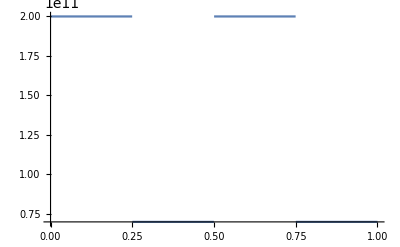

```mathematica
Plot[Y[x],{x,0,1}]
```

```mathematica
rho[x_]:=Piecewise[{{7800, 0<=x<0.25},{7800,0.5≤ x<0.75}, {2700,0.25≤ x<0.5}, {2700,0.75≤ x<=1}}];
```

```mathematica
f[x_]:=Piecewise[{{10^5*Cos[4*Pi*(x-0.5)],0.375≤ x<0.625},{0,True}}];
```

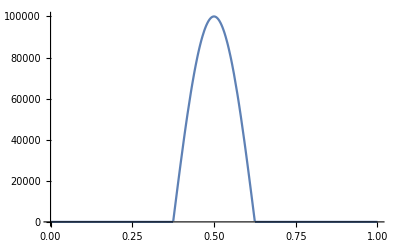

```mathematica
Plot[f[x],{x,0,1}]
```

```mathematica
A = 10^-4*Pi;
g=9.81;
m=320.0;
```

```mathematica
u[x_]:=
```